```mathematica
da= 1/2 {{0.05, 0.1}, {0.05,-0.1},{-0.05, -0.1},{-0.05,0.1}}
```

{{0.025,0.05},{0.025,-0.05},{-0.025,-0.05},{-0.025,0.05}}

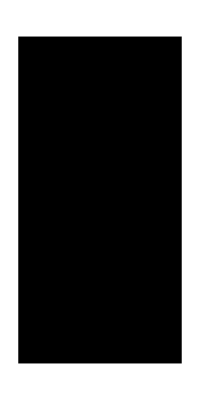

```mathematica
Polygon[%]//Graphics
```

```mathematica
dat=Composition[TranslationTransform[{0.15,0}],RotationTransform[ Pi/4],TranslationTransform[{0.05,0}]][da]
```

{{0.167678,0.0883883},{0.238388,0.0176777},{0.203033,-0.0176777},{0.132322,0.053033}}

```mathematica
dbt=Composition[TranslationTransform[{0.15,0}],RotationTransform[ Pi/4],TranslationTransform[{-0.05,0}]][da]
```

{{0.096967,0.0176777},{0.167678,-0.053033},{0.132322,-0.0883883},{0.0616117,-0.0176777}}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/pbialas/PET/tools/src/2d/geometry

```mathematica
Export["gate_volume_test.txt", Join[dat, dbt], "Table"]
```

gate_volume_test.txt

```mathematica
LinearRepeat[poly_, tr_, n_, v_]:= Module[{last = (n-1) v, t},
t = Composition[tr,TranslationTransform[-last/2]];
t/@TranslationTransform[#][poly]&/@Table[v*i,{i,0,n-1}]
]
```

```mathematica
pr=LinearRepeat[da,TranslationTransform[{0,0}],4 , {0.1, 0.0}]
```

{{{-0.125,0.05},{-0.125,-0.05},{-0.175,-0.05},{-0.175,0.05}},{{-0.025,0.05},{-0.025,-0.05},{-0.075,-0.05},{-0.075,0.05}},{{0.075,0.05},{0.075,-0.05},{0.025,-0.05},{0.025,0.05}},{{0.175,0.05},{0.175,-0.05},{0.125,-0.05},{0.125,0.05}}}

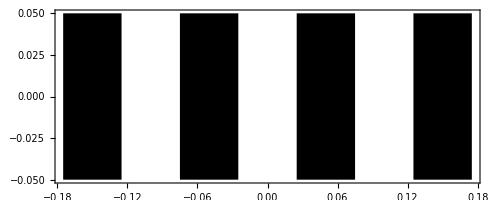

```mathematica
Graphics[Polygon/@pr, Frame->True]
```

```mathematica
Export["gate_volume_s_repeater_test.txt",Flatten[pr,1],"Table"]
```

gate_volume_s_repeater_test.txt